```mathematica
Define symmetric quantization rho
```

```mathematica
CleanSlate;
$MinPrecision=MachinePrecision;
  ρz[z_] := z/(1 + Sqrt[1 - z])^2; 
 ρzb[z_] := ρz[Conjugate[z]]; 
 (*error estimates*)
    ρintErrorEstimateG[d_, DDs_, z_, γ_] := (2^(γ + 4*d)*β^(γ - 4*d)*Gamma[1 - γ + 4*d, β*DDs])/(Gamma[1 - γ + 4*d]*(1 - r^2)^γ)/.  {r -> Abs[ρz[z]], β -> -Log[Abs[ρz[z]]]}; 
      ρintErrorEstimateFt[d_, DDs_, z_, γ_] := 
     v^d*ρintErrorEstimateG[d, DDs, z, γ] + u^d*ρintErrorEstimateG[d, DDs, 1 - z, γ] /. {u -> z*Conjugate[z], v -> (1 - z)*(1 - Conjugate[z])}; 
     (*coefficients and prefactors*)
    kfunctAna[β_, x_] := Exp[(β/2)*Log[4*((1 - Sqrt[1 - x])^2/x)]]*(x/(2*(1 - x)^(1/4)*(1 - Sqrt[1 - x]))); 
    ConformalBlockAna[DD_, l_, z_] := ((-1)^l/2^l)*((z*Conjugate[z])/(z - Conjugate[z]))*(kfunctAna[DD + l, z]*kfunctAna[DD - l - 2, Conjugate[z]] - 
       kfunctAna[DD + l, Conjugate[z]]*kfunctAna[DD - l - 2, z]);
       (*derivatives*)
       FAnaDer[DD_, l_, z_] := (1/(z - Conjugate[z]))*(-1)^(2*l)*(1 - z)*z*
      (1 - Conjugate[z])*Conjugate[z]*(-((2^(-5 + 2*DD)*((1 - Sqrt[z])/(1 + Sqrt[z]))^((1/2)*(-2*l + DD))*(1 - z)*
          ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^((1/2)*(-2*l + DD))*(-((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) - 
           Sqrt[z]*(((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) + ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l)) + 
           ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l) + (((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) + 
             Sqrt[z]*(((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) - ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l)) + 
             ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l))*Sqrt[Conjugate[z]])*(1 - Conjugate[z])*
          (Log[16] + Log[-((-1 + Sqrt[z])/(1 + Sqrt[z]))] + Log[-((-1 + Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))]))/
         ((-1 + Sqrt[z])^2*z^(1/4)*(-1 + Sqrt[Conjugate[z]])^2*Conjugate[z]^(1/4))) + (2^(-5 + 2*DD)*((-1 + Sqrt[1 - z])^2/z)^((1/2)*(-2*l + DD))*z*
         ((-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z])^((1/2)*(-2*l + DD))*Conjugate[z]*(-2*z*(-((-2 + 2*Sqrt[1 - z] + z)/z))^(2*l)*
           (-1 + Sqrt[1 - Conjugate[z]]) + Conjugate[z]*(2*(-1 + Sqrt[1 - z])*(-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^(2*l) + 
            z*(-(-((-2 + 2*Sqrt[1 - z] + z)/z))^(2*l) + (-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^(2*l))))*
         (Log[16] + Log[(-1 + Sqrt[1 - z])^2/z] + Log[(-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z]]))/((-1 + Sqrt[1 - z])^3*(1 - z)^(1/4)*
         (-1 + Sqrt[1 - Conjugate[z]])^3*(1 - Conjugate[z])^(1/4))); 
	 ConformalBlockAnaDer[DD_, l_, z_] := 
     -((I*(-1)^l*2^(-6 - l + 2*DD)*((-1 + Sqrt[1 - z])^2/z)^((1/2)*(-l + DD))*Abs[z]^4*((-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z])^
         ((1/2)*(-l + DD))*(2*z*(-1 + Sqrt[1 - Conjugate[z]])*(-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^l + 
         Conjugate[z]*(-2*(-1 + Sqrt[1 - z])*(-((-2 + 2*Sqrt[1 - z] + z)/z))^l + z*(-(-((-2 + 2*Sqrt[1 - z] + z)/z))^l + 
             (-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^l)))*(Log[(16*(-1 + Sqrt[1 - z])^2)/z] + 
         Log[(-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z]]))/((-1 + Sqrt[1 - z])^3*(1 - z)^(1/4)*(-1 + Sqrt[1 - Conjugate[z]])^3*
        (1 - Conjugate[z])^(1/4)*Im[z])); 
	kfunct[β_, x_] := kfunct[β, x] = x^(β/2)*Hypergeometric2F1[β/2, β/2, β, x]; 
    ConformalBlock[DD_, l_, z_] := ((-1)^l/2^l)*((z*Conjugate[z])/(z - Conjugate[z]))*(kfunct[DD + l, z]*kfunct[DD - l - 2, Conjugate[z]] - 
       kfunct[DD + l, Conjugate[z]]*kfunct[DD - l - 2, z]); 
      
      (*random sample of z around (1/2+I0)*)
           Sample[nz_,var_,seed_] := Module[{imax}, SeedRandom[seed];Table[Abs[RandomVariate[NormalDistribution[0, var]]]+
           1/2+I Abs[RandomVariate[NormalDistribution[0, var]]],{imax,1,nz}]]; 
(*Exponential factor to renormalize*)
dimExpFactor[a_,b_]:=Log[4(1-Sqrt[1/2 -a -b])^2/(1/2 + a +b)];

renomFactor[dim_]:=Exp[-(dim-1)dimExpFactor[0,0]];
(*renomFactor[dim_]:=1;*)
(*Conformal Blocks*)
qQGen[Δϕ_,Δ_,L_,zsample_]:=renomFactor[Δ] (((1 - zsample)*(1 - Conjugate[zsample]))^Δϕ    ConformalBlock[Δ, L , zsample]- ((zsample)*( Conjugate[zsample]))^Δϕ ConformalBlock[Δ, L,1- zsample])2^(L);
qQGenDims[Δϕ_,ΔL_,z_]:=qQGen[1,#1[[1]],#1[[2]], z]&/@ΔL
MetroGoFixedSelectiveDir[Δϕ_,ΔLOriginal_,Ndit_,prec_,betad_,seed_,sigmaMC_,dcross_,lmax_,idTag_,initialOps_]:=Block[{itd, DDldata, sigmaz, sigmaD, Action=100000000, Actionnew=0, Action0, DDldatafixed, QQ0, QQ1, str, Lmax, Nvmax, rr, metcheck, sigmaDini, 
    zsample, Idsample, Nz, PP0, PP1, lr, nr, Errvect, Factor, Factor0, ppm, DDldataEx, PPEx, QQEx, Idsampleold, ip, nvmax, QQFold,  
    IdsampleEx,zOPE,QQOPE,Calc,coeffTemp,Ident,OPEcoeff,ActionTot,  TotD ,DDldataold,QQold,ΔLOld,dimToVary,PP,QQsave,ΔL,dw,smearedaction}, 
    (*precision*)
SetOptions[{RandomReal,RandomVariate},WorkingPrecision->prec];
$MaxPrecision=prec;
$MinPrecision=prec;

    SeedRandom[seed];
    Nz=Length[ΔLOriginal]+1;
  zsample = Sample[Nz,1/100,seed]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
    ΔL = ΔLOriginal;
  ΔL[[All,1]] = SetPrecision[ΔL[[All,1]],prec];
  

    QQ0 = qQGenDims[Δϕ,ΔL,zsample];
     
    (*Monte Carlo Iteration*)
TotD =   Reap[ Do[
$MinPrecision=prec;
          ΔLOld=ΔL;
          QQold=QQ0;  

(*let every successive run start by varying only the new operator*)
        If[it<Ndit/10&& Nz!=initialOps+1,dimToVary=Nz-1,  dimToVary = RandomInteger[{1,lmax}]];
       (*Shift one dimension by a random amount*)       
          ΔL[[dimToVary,1]] = ΔL[[dimToVary,1]]+ RandomVariate[NormalDistribution[0, sigmaMC]];
(*Reevaluate coefficients*)
           QQ0[[dimToVary]] = qQGen[Δϕ,ΔL[[dimToVary]][[1]],ΔL[[dimToVary]][[2]],zsample];
          
    (*Coefficients for LES and action thence*)
          PP = Join[QQ0, {Idsample}]; 
          Actionnew = Log[Det[PP]^2]; 
QQsave=QQ0;
(*Brot noch schmieren? *)
smearedaction=Reap[Table[
           QQ0[[dimToVary]] =qQGen[Δϕ,ΔL[[dimToVary]][[1]]+dcross,ΔL[[dimToVary]][[2]],zsample];  PP = Join[QQ0, {Idsample}]; 
          Sow[ Log[Det[PP]^2]];
           QQ0[[dimToVary]] =qQGen[Δϕ,ΔL[[dimToVary]][[1]]-dcross,ΔL[[dimToVary]][[2]],zsample];  PP = Join[QQ0, {Idsample}]; 
          Sow[ Log[Det[PP]^2]];QQ0=QQsave;,{dimToVary,1,lmax}]];

 Actionnew =Actionnew +Total[smearedaction[[2]]//Flatten] ;
         

          metcheck = Exp[(-betad)*(Actionnew - Action)];
          rr = RandomReal[{0, 1}];
          If[metcheck>rr, Action = Actionnew,ΔL=ΔLOld;QQ0=QQold];
          
$MinPrecision=10;
   dw=ΔL[[All,1]];
          Sow[ {it, dw, N[Action,10]}],
     {it, 1, Ndit}]]; 
$MinPrecision=3;
      Export["Res-fixed_Param_Nit="<>ToString[Ndit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[betad,3]]<>"sigmaMC="<>ToString[N[sigmaMC,3]]<>"dcross="<>ToString[N[dcross,3]]<>"seed="<>ToString[seed]<>"id="<>idTag<>".txt", TotD[[2]]];]

weightedLeastSquares[qq0_,id_,w_]:=Block[{rhovec,nu,s,r},
rhovec=Inverse[Transpose[qq0].w.qq0].Transpose[qq0] . w.id;
nu = Dimensions[w][[1]]-Length[rhovec];
r=(qq0.rhovec-id);
s=r.w.r;
Return[{rhovec,(*(Diagonal[Inverse[Transpose[qq0].w.qq0]])^(-1/2),r,*) s/nu}]];

metroReturnAvg[prec_,nit_,β_,ΔL_,seed_,initialOps_,idtag_]:=Block[{data},
MetroGoFixedSelectiveDir[1,ΔL,nit,prec,β,seed,1/10,1/3,Length[ΔL],ToString[Length[ΔL]]<>"id"<>idtag,initialOps];
data= Get["Res-fixed_Param_Nit="<>ToString[nit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[β,3]]<>"sigmaMC="<>ToString[N[1/10,3]]<>"dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]<>"id="<>ToString[Length[ΔL]]<>"id"<>idtag<>".txt"];
Export["Plot-fixed_Param_Nit="<>ToString[nit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[β,3]]<>"sigmaMC="<>ToString[N[1/10,3]]<>"dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]<>"id="<>ToString[Length[ΔL]]<>"id"<>idtag<>".pdf",ListPlot[Table[data[[All,2]][[All,i]],{i,1,Length[ΔL]}],Joined->True,GridLines->Automatic,PlotStyle->Thin,PlotLabel->ToString[Length[ΔL]]<>"id"<>idtag<>"Nit="<>ToString[nit]<>" prec="<>ToString[prec]<>" beta="<>ToString[N[β,3]]<>" sigmaMC="<>ToString[N[1/10,3]]<>" dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]]];
Export["zoom-Plot-fixed_Param_Nit="<>ToString[nit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[β,3]]<>"sigmaMC="<>ToString[N[1/10,3]]<>"dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]<>"id="<>ToString[Length[ΔL]]<>"id"<>idtag<>".pdf",ListPlot[Table[data[[All,2]][[All,i]]-2i+1,{i,1,Length[ΔL]}],Joined->True,GridLines->Automatic,PlotStyle->Thin,PlotRange->{{0,nit},{0,2}},PlotLabel->ToString[Length[ΔL]]<>"id"<>idtag<>"Nit="<>ToString[nit]<>" prec="<>ToString[prec]<>" beta="<>ToString[N[β,3]]<>" sigmaMC="<>ToString[N[1/10,3]]<>" dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]]];
{Mean[data[[All,2]][[nit-100;;nit,1;;Length[ΔL]]]],StandardDeviation[data[[All,2]][[nit-100;;nit,1;;Length[ΔL]]]]}]

checkMetroWeighted[Δϕ_,ΔLOriginal_,prec_,seed_,Nz_,sigmaz_]:=Block[{itd, DDldata,  sigmaD, Action=100000000, Actionnew=0, Action0, DDldatafixed, QQ0, QQ1, str, Lmax, Nvmax, rr, metcheck, sigmaDini, 
    zsample, Idsample, PP0, PP1, lr, nr, Errvect, Factor, Factor0, ppm, DDldataEx, PPEx, QQEx, Idsampleold, ip, nvmax, QQFold,  
    ΔLOld,dimToVary,PP,QQsave,ΔL=ΔLOriginal,dw,smearedaction,ρ,rhovec,eqs,rhosol,last,check,results,indices,rhopos,meanrho,sigmarho,finalcheck,errSample}, 
    (*precision*)
SetOptions[{RandomReal,RandomVariate,NSolve},WorkingPrecision->prec];
$MaxPrecision=prec;
$MinPrecision=prec;

    SeedRandom[seed];
  zsample = Sample[Nz,sigmaz,seed]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
    ΔL = ΔLOriginal;
  ΔL[[All,1]] = SetPrecision[ΔL[[All,1]],prec];
  

    QQ0 = qQGenDims[Δϕ,ΔL,zsample];
errSample=Table[ ρintErrorEstimateFt[Δϕ,ΔLOriginal[[-1,1]],zsample[[i]],1],{i,1,Nz}];
results=weightedLeastSquares[(QQ0//Transpose),Idsample,DiagonalMatrix[errSample^(-2)]];
finalcheck=Abs[results[[1]].QQ0-Idsample]<errSample//Thread;
Return[{results,And@@finalcheck}];
]
mcIterator[initialOps_,finalOps_,ΔLinitial_,β_,nz_,prec_,seed_,nits_,runid_]:=Block[{ΔL=ΔLinitial,results},
results=Reap[Table[ΔL[[1;;it,1]]=Sow[metroReturnAvg[prec,nits[[it-initialOps+1]],β[[it-initialOps+1]],ΔL[[1;;it]],seed,initialOps,runid]][[1]];
Sow[checkMetroWeighted[1,ΔL[[1;;it]],prec,seed,nz,runid]];
,{it,initialOps,finalOps}]];
Export["averages_n_checks"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".txt", results];
]
mcPlotDimsAndOPEs[initialOps_,finalOps_,nz_,prec_,seed_,runid_]:=Block[{data,dims,opes,mcDims,mcOpes,refDims,refOpes,nrecs=(finalOps-initialOps) +1},
data= Get["averages_n_checks"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".txt"];
dims=data[[1,Range[1,2nrecs -1,2]]];
opes=data[[1,Range[2,2nrecs ,2]]];
mcDims=ListPlot[dims[[;;,1,1;;4]]//Transpose,PlotLegends->{"l=0","l=2","l=4","l=6"},PlotRange->All];
refDims=Plot[{2,4,6,8},{x,0,nrecs},PlotStyle->Dashed];
mcOpes=ListPlot[opes[[;;,1,1,1;;4]]//Transpose,PlotLegends->{"l=0","l=2","l=4","l=6"},PlotRange->All];
refOpes=Plot[{2,1/3},{x,0,nrecs},PlotStyle->Dashed];
Export["dims-plot"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".pdf",Show[mcDims,refDims],PlotLabel->"Dims_from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]];
Export["opes-plot"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".pdf",Show[mcOpes,refOpes],PlotLabel->"OPEs_from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]];
Return[opes[[;;,2]]]
]
deltaFree[n_]:={2#,2#-2}&/@Range[1,n,1];
opeFreeRen[n_]:=(renomFactor[2#])^(-1) 2((2#-2)!)^2/(2(2#-2))!&/@Range[1,n,1];
```

```mathematica
(*βvec={1/7,1/9,1/10,1/11,1/12,1/13};*)
(*initial=4;*)
(*final=9;*)
(*nvec={3000,2000,2000,2000,2000,2000};*)
(*Table[*)
(*ΔLinitial={#+2i/10,#-2}&/@Range[2,18,2];*)
(*ParallelTable[mcIterator[initial,final,ΔLinitial,βvec,1000,88,seed,nvec,ToString[i]];mcPlotDimsAndOPEs[initial,final,1000,88,seed,ToString[i]],{seed,555,558}],{i,2,10}];*)
```

```mathematica
(*βvec={1/7,1/9,1/10,1/11,1/12,1/13};*)
(*nvec={3000,2000,2000,2000,2000,2000};*)
(*ΔLinitial={#+1,#-2}&/@Range[2,18,2];*)
(*initial=4*)
(*final=9*)
(*Table[mcIterator[initial,final,ΔLinitial,βvec,1000,88,seed,nvec,"anche_OPEs"];mcPlotDimsAndOPEs[initial,final,1000,88,seed,"anche_OPEs"],{seed,566,585}];*)
```

```mathematica
c=Table[{{nop,2+isigmaz/5,IntegerPart[10^(inz/3)]},checkMetroWeighted[1,deltaFree[nop],110,123,IntegerPart[10^(inz/3)],10^-(2+isigmaz/5)]},{nop,4,10},{isigmaz,1,1},{inz,5,9}];
Print[Dimensions[c]];
Export["scanningOPEsolverhighnz-refinementin_sigmaz-noren.txt",c]
```

{7,1,5,2}

scanningOPEsolverhighnz-refinementin_sigmaz-noren.txt

```mathematica
Table[nops=Table[((c[[i,isigmaz,inz-8,2,1,1]]-opeFreeRen[i+3])/opeFreeRen[i+3])//Abs//Log,{i,1,7}];
Export["plot_error_vsnops_sigmaz=e-"<>ToString[isigmaz]<>"nZ="<>ToString[IntegerPart[10^(inz/3)]]<>".pdf",ListPlot[nops,Joined->True,PlotRange->All,PlotLegends->Range[4,10]]],{isigmaz,1,1},{inz,5,1}];
```

```mathematica
.
```

```mathematica
opeFreeRen[10]//N[#,16]&
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

{1.37258300203047921917298041264483074288524999396883082917312419214828034460628737839379945,0.107746856178060456144838513517536002623332770424210722824924600506165496586821983421282071,0.00434985779123783926385603548801203405620234583718724331763004088806303771681978597502884918,0.000155209524714349057538825346929606959682028255955146402887197662305490799933856487023069281,5.24842547270864475024379495515661529009771740440326633542311031384208594731947696588461679×10^-6,1.72197273888787647074919783508837749408166080919427809228549793816188495609121356403851427×10^-7,5.54128289124616071504541353827163978026436499179924916693432294861213243480547242119956502×10^-9,1.75928089823202471701257863969421911646375988543557721073551777235318710187370040781388197×10^-10,5.53024010329181558303406311048481483425431404936258872893030729204417552224804971382648872×10^-12,1.72520488603068371342306570847829587463522257771554951425448620915745781398461633551323129×10^-13}

```mathematica
(*{{5,2,IntegerPart[10^(5/2)]},checkMetroWeighted[1,deltaFree[5],90,123,IntegerPart[10^(5/2)],10^(-2)]}*)
```

```mathematica
{a[[7,2,1,2,1]],a[[7,2,1,1]]}
```

{{{1.37257970651260166302466383575183274085465765330150071169283778633436034309969250130633089,0.107747361272111337405386537139064438674560790098177394637568833924946355787988059722407516,0.00434974517555402600687982812360566294989987254139640543164314876667128251101161848112151455,0.000155237072557288729831721340340089082343156928005776544907928144404284892139218521966947662,5.24193234262788341915153253604505105941935728989643853536264081507562560255419768519667433×10^-6,1.73571604121340870707185850667045609577038884821233177185124548763208779883500066810691658×10^-7,5.29464689979747413477036096335278423092225273014452959540849810452872144656506014096929695×10^-9,2.11173099707007706742880935973043068000090489419640178578267921818373154206326159339647918×10^-10,1.85934804817775880571145023064617751919278703222469724040573266490151919144453422236106152×10^-12,4.08338341939276916829200311477766089318008459914519219872746972659280136205315957232970014×10^-13},4.99733829764169515334039671565362225121250328853066577650992640055881717691293237259958346×10^-50},{10,2,46}}

```mathematica
renomFactor[2]//N
```

1.45711

```mathematica
2/renomFactor[2]//N
```

1.37258

```mathematica
a[[7,2,1,2,1]]
```

{{1.37257970651260166302466383575183274085465765330150071169283778633436034309969250130633089,0.107747361272111337405386537139064438674560790098177394637568833924946355787988059722407516,0.00434974517555402600687982812360566294989987254139640543164314876667128251101161848112151455,0.000155237072557288729831721340340089082343156928005776544907928144404284892139218521966947662,5.24193234262788341915153253604505105941935728989643853536264081507562560255419768519667433×10^-6,1.73571604121340870707185850667045609577038884821233177185124548763208779883500066810691658×10^-7,5.29464689979747413477036096335278423092225273014452959540849810452872144656506014096929695×10^-9,2.11173099707007706742880935973043068000090489419640178578267921818373154206326159339647918×10^-10,1.85934804817775880571145023064617751919278703222469724040573266490151919144453422236106152×10^-12,4.08338341939276916829200311477766089318008459914519219872746972659280136205315957232970014×10^-13},4.99733829764169515334039671565362225121250328853066577650992640055881717691293237259958346×10^-50}

```mathematica
Table[nops=Table[((a[[i,j,2,2,1,1]]-opeFreeRen[i+3])/opeFreeRen[i+3])//Abs//Log,{i,1,7}];
Export["plot_error_vsnops_sigmaz=e-"<>ToString[j]<>".pdf",ListPlot[nops,Joined->True,PlotRange->All,PlotLegends->Range[4,10]]],{j,1,4}]
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

{plot_error_vsnops_sigmaz=e-1.pdf,plot_error_vsnops_sigmaz=e-2.pdf,plot_error_vsnops_sigmaz=e-3.pdf,plot_error_vsnops_sigmaz=e-4.pdf}

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

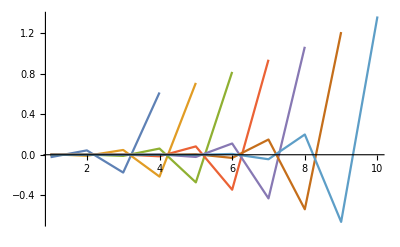

```mathematica
Table[nops=Table[((a[[i,isigmaz,inz-8,2,1,1]]-opeFreeRen[i+3])/opeFreeRen[i+3])//Abs//Log,{i,1,7}];
Export["plot_error_vsnops_sigmaz=e-"<>ToString[isigmaz]<>"nZ="<>ToString[IntegerPart[10^(inz/3)]]<>".pdf",ListPlot[nops,Joined->True,PlotRange->All,PlotLegends->Range[4,10]]],{isigmaz,1,4},{inz,9,12}];
```

```mathematica
a[[7,2,3,2,1,1]]
```

{1.3725797037512316326788853387918766508753487875513983596256476422009818740310230155311199189450669016778598017,0.10774736169354698837920603471367372784676778243224752192707941120166914420440781384009160166355479963752398871,0.0043497450829344342291935399344754481098459039767540833623473409826807556597738136825918462393316540320321653389,0.00015523709454328269027726628597491357013278921221883939774958189524877195235434346670281963112194121124958562632,5.2419274195655273683796200906881107673939439728126042685708263631274736732010807952392237673278054485106775736×10^-6,1.7357256658058836461146259131294885541616517209382910942238382481498294317281993823737659000529478874041780862×10^-7,5.2944933609296274110343770525736139815177353626793563013660960047455625790236009103843527632666731225038019525×10^-9,2.1119153350218394807234768419737178023123649556396398226568462102602620094134034253293956319678005373527708693×10^-10,1.8578830717959333346863058883825284276850835638703879586119351830665383081911995489959570060550667465441261641×10^-12,4.0839573598870975608259852182476620052589535829303378450266812439376913169100088066102721240872301822437722183×10^-13}

```mathematica
data =Get["scanningOPEsolver.txt"];
chi=data[[]];
```

```mathematica
Dimensions[data]
```

{4,5,2}

```mathematica
b//Dimensions
```

{7,4,8,2}

```mathematica
logNz=(#/3)&/@Range[5,12]
```

{5/3,2,7/3,8/3,3,10/3,11/3,4}

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

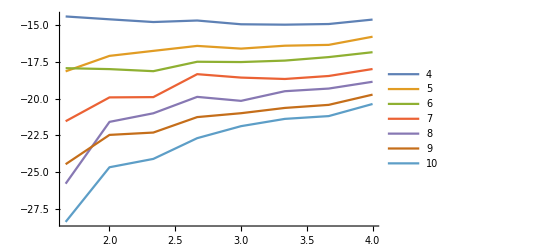
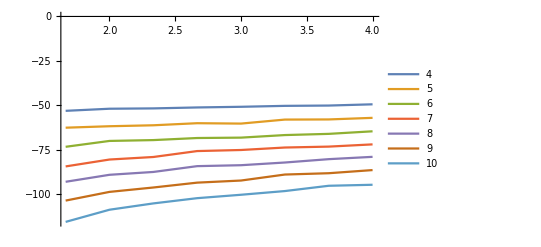
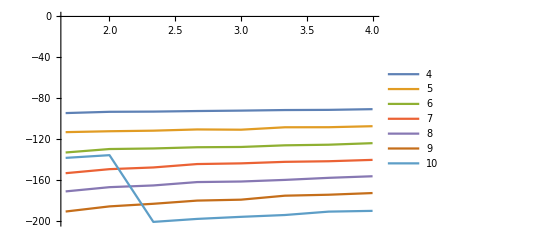
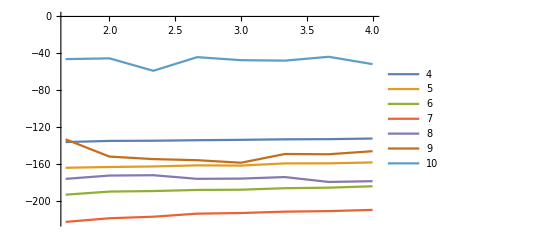

```mathematica
plots=ListPlot[Table[({logNz,b[[i,#,;;,2,1,2]]//Log}//Transpose),{i,1,7}],Joined->True,PlotRange->All,PlotLegends->Range[4,10]]&/@Range[1,4]
```

```mathematica
plots[[1]]
```

-Graphics-

```mathematica
Table[Export["plot_chivsNz_sigmaz=e-"<>ToString[i]<>".pdf",plots[[i]]],{i,1,4}]
```

{plot_chivsNz_sigmaz=e-1.pdf,plot_chivsNz_sigmaz=e-2.pdf,plot_chivsNz_sigmaz=e-3.pdf,plot_chivsNz_sigmaz=e-4.pdf}

```mathematica
#
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

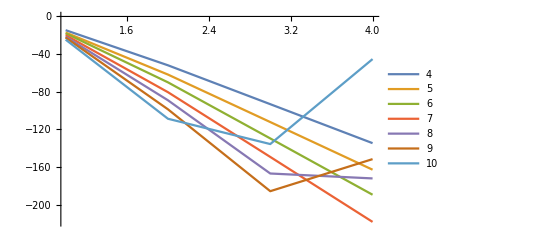

```mathematica
ListPlot[b[[;;,;;,2,2,1,2]]//Log,Joined->True,PlotRange->All,PlotLegends->Range[4,10]]
```